```mathematica
(* MAKE this Flashy dashy *)
```

```mathematica
BOARD={{Table[{ FaceForm[RGBColor[255/255, 222/255,173/255]], Rectangle[{i,j},{i+1,j+1}]},{i, 0,9,2},{j,0,7,2}]},
{Table[{ FaceForm[RGBColor[255/255, 222/255,173/255]], Rectangle[{i,j},{i+1,j+1}]},{i, 1,10,2},{j,1,8,2}]},{Line[{{0,0},{0,8},{10,8},{10,0},{0,0}}]}
};
(* 1 king, 2 switches, 2 defenders, 7 deflectors, 1 laser *)(* "s"= switch, d= deflector, "D"= defender, "L"= laser, "k"= King*)
CURIOSITY={{{"s",{3,0},1},{"D",{4,0},1},{"k",{5,0},1},{"D",{6,0},1},{"L",{10,0},1},{"d",{4,3},3},{"d",{2,4},4},{"s",{4,4},1},{"d",{10,4},3},{"d",{2,5},3},{"d",{4,5},3},{"d",{10,5},4},{"d",{4,6},4}},
{{"s",{8,8},1},{"D",{7,8},3},{"k",{6,8},1},{"D",{5,8},3},{"L",{0,8},2},{"d",{6,6},1},{"d",{9,5},2},{"s",{6,5},1},{"d",{0,5},1},{"d",{9,4},1},{"d",{6,4},4},{"d",{0,4},2},{"d",{7,3},2}}};
```

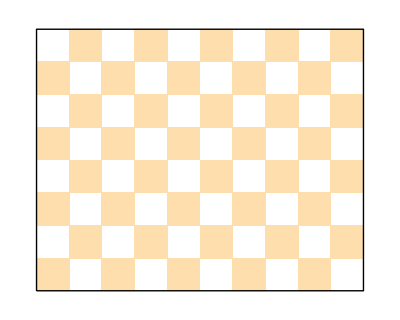

```mathematica
Graphics[BOARD]
```

```mathematica
processBoard[letter_,coords_, rotation_]:=
```